# Θ_lm^2 in the Hydrogen atom

SphericalHarmonicY[l,m,θ,ϕ]gives the spherical harmonicY_l^m(θ,ϕ). It is the angular solution found in the Hydrogen atom.


The spherical harmonics are orthonormal with respect to integration over the surface of the unit sphere.

Forl≥0,Y_l^m(θ,ϕ)=√((2l+1)/(4π))√((l-m)!/(l+m)!)P_l^m(cos(θ))e^imϕwhere P_l^m is the associated Legendre function.

Forl≤-1,Y_l^m(θ,ϕ)=Y_(-(l+1))^m(θ,ϕ)

#### Examples: Spherical Harmonics

```mathematica
Y00=SphericalHarmonicY[0,0,θ,ϕ];
Y10=SphericalHarmonicY[1,0,θ,ϕ];
Y11=SphericalHarmonicY[1,1,θ,ϕ]
Y20=SphericalHarmonicY[2,0,θ,ϕ];
Y21=SphericalHarmonicY[2,1,θ,ϕ];
Y22=SphericalHarmonicY[2,2,θ,ϕ];
Y30=SphericalHarmonicY[3,0,θ,ϕ];
Y31=SphericalHarmonicY[3,1,θ,ϕ];
Y32=SphericalHarmonicY[3,2,θ,ϕ];
Y33=SphericalHarmonicY[3,3,θ,ϕ];
```

-1/2 ⅇ^(ⅈ ϕ) √(3/(2 π)) Sin[θ]

#### The usual Θ_lm^2=Y_lm*Y_lm^*

```mathematica
Subscript[Θ, 00]=Simplify[Y00*Conjugate[Y00],Element[{θ,ϕ}, Reals]];
Subscript[Θ, 10]=Simplify[Y10*Conjugate[Y10],Element[{θ,ϕ}, Reals]];
Subscript[Θ, 11]=Simplify[Y11*Conjugate[Y11],Element[{θ,ϕ}, Reals]]
Subscript[Θ, 20]=Simplify[Y20*Conjugate[Y20],Element[{θ,ϕ}, Reals]];
Subscript[Θ, 21]=Simplify[Y21*Conjugate[Y21],Element[{θ,ϕ}, Reals]];
Subscript[Θ, 22]=Simplify[Y22*Conjugate[Y22],Element[{θ,ϕ}, Reals]];
Subscript[Θ, 30]=Simplify[Y30*Conjugate[Y30],Element[{θ,ϕ}, Reals]];
Subscript[Θ, 31]=Simplify[Y31*Conjugate[Y31],Element[{θ,ϕ}, Reals]];
Subscript[Θ, 32]=Simplify[Y32*Conjugate[Y32],Element[{θ,ϕ}, Reals]];
Subscript[Θ, 33]=Simplify[Y33*Conjugate[Y33],Element[{θ,ϕ}, Reals]];
```

(3 Sin[θ]^2)/(8 π)

```mathematica
PolarPlot[Subscript[Θ, 11],{θ,0,2Pi}]
```

-Graphics-

```mathematica
Grid[{{"l",Subscript[Θ, 00],,,},{"m",Subscript[Θ, 10],Subscript[Θ, 11],,},{,Subscript[Θ, 20],Subscript[Θ, 21],Subscript[Θ, 22],},{,Subscript[Θ, 30],Subscript[Θ, 31],Subscript[Θ, 32],Subscript[Θ, 33]}},Frame->All]
```

l | 1/(4 π) |  |  | 
m | (3 Cos[θ]^2)/(4 π) | (3 Sin[θ]^2)/(8 π) |  | 
 | (5 (1+3 Cos[2 θ])^2)/(64 π) | (15 Sin[2 θ]^2)/(32 π) | (15 Sin[θ]^4)/(32 π) | 
 | (7 Cos[θ]^2 (1-5 Cos[2 θ])^2)/(64 π) | (21 (3+5 Cos[2 θ])^2 Sin[θ]^2)/(256 π) | (105 Cos[θ]^2 Sin[θ]^4)/(32 π) | (35 Sin[θ]^6)/(64 π)

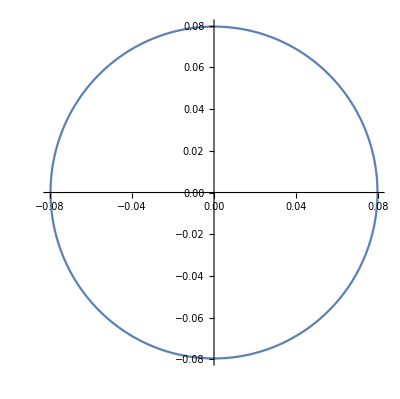
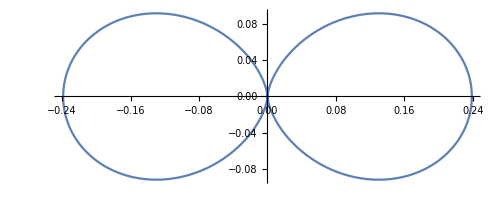
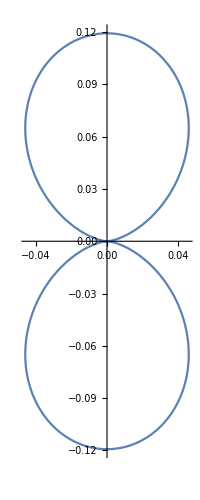
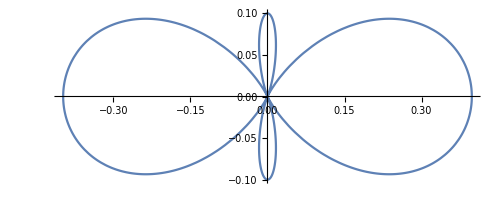
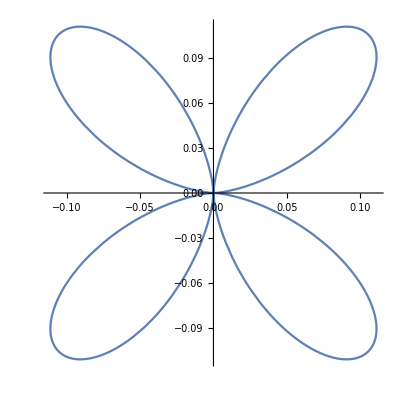
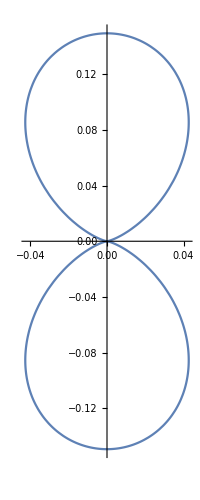
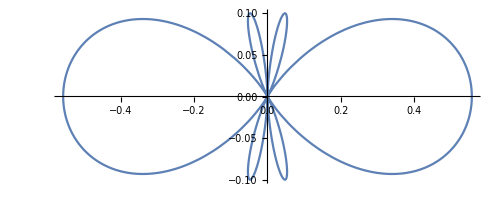
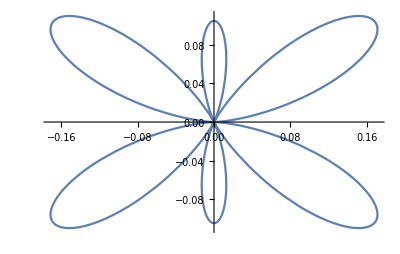
l | -Graphics- |  |  | 
m | -Graphics- | -Graphics- |  | 
 | -Graphics- | -Graphics- | -Graphics- | 
 | -Graphics- | -Graphics- | (105 Cos[θ]^2 Sin[θ]^4)/(32 π) | (35 Sin[θ]^6)/(64 π)

```mathematica
Grid[{{"l",PolarPlot[Subscript[Θ, 00],{θ,0,2Pi}],,,},{"m",PolarPlot[Subscript[Θ, 10],{θ,0,2Pi}],PolarPlot[Subscript[Θ, 11],{θ,0,2Pi}],,},{,PolarPlot[Subscript[Θ, 20],{θ,0,2Pi}],PolarPlot[Subscript[Θ, 21],{θ,0,2Pi}],PolarPlot[Subscript[Θ, 22],{θ,0,2Pi}],},{,PolarPlot[Subscript[Θ, 30],{θ,0,2Pi}],PolarPlot[Subscript[Θ, 31],{θ,0,2Pi}],Subscript[Θ, 32],Subscript[Θ, 33]}},Frame->All]
```

#### Polar 3 D

```mathematica
SphericalPlot3D[Subscript[Θ, 11],{θ,0,Pi},{ϕ,0,2Pi}]
```

-Graphics3D-

```mathematica
SphericalPlot3D[Subscript[Θ, 30],{θ,0,Pi},{ϕ,0,2Pi}]
```

-Graphics3D-

```mathematica
SphericalPlot3D[Subscript[Θ, 31],{θ,0,Pi},{ϕ,0,2Pi}]
```

-Graphics3D-

```mathematica
SphericalPlot3D[1+2Cos[2θ],{θ,0,Pi},{ϕ,0,2Pi}]
```

-Graphics3D-

Plot an eigenfunction to the Laplace equation in spherical coordinates :

```mathematica
GraphicsGrid@Table[SphericalPlot3D[Evaluate@Abs@SphericalHarmonicY[l,m,θ,ϕ],{θ,0,Pi},{ϕ,0,2Pi},PlotRange->0.6,Mesh->None,Boxed->False,Axes->None],{l,0,3},{m,0,l}]
```

-Graphics-